```mathematica
Off[General::munfl,FindFit::cvmit,FindFit::sszero,General::stop]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/Downloads

```mathematica
(* Johannes fitting parameters *)
LCD={{0.0025, 0.01085409,-1.106057,-1.159333},
{0.0900, 0.01085514,-13.493590, 2.150388},
{0.3025, 0.01085640,-39.797327, 24.965545},
{0.6400, 0.01085554,-80.013554, 81.336340},
{1.1025, 0.01085210,-134.141484, 191.491264},
{1.6900, 0.01085481,-202.185387, 379.175010},
{2.4025, 0.01085130,-284.138103, 683.999621},
{3.2400, 0.01086136,-380.015170, 1143.332900},
{4.2025, 0.01085691,-489.792808, 1884.506079},
{5.2900, 0.01085517,-613.485357, 2977.884003},
{6.5025, 0.01084950,-751.085499, 4589.004608},
{7.8400, 0.01084884,-902.604164, 7067.645881},
{9.3025, 0.01084997,-1068.038344, 10667.304476},
{10.8900, 0.01085217,-1247.387431, 16133.941591},
{12.6025, 0.01085409,-1440.650123, 24382.008195},
{14.4400, 0.01084667,-1647.808037, 36688.658380},
{16.4025, 0.01085322,-1868.905655, 52963.123627},
{18.4900, 0.01087420,-2103.948323, 80952.129573},
{20.7025, 0.01085536,-2352.819143, 119013.695269},
{23.0400, 0.01085344,-2615.638250, 190732.889176}};
```

## Finite differences

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ]:=Block[{p,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
p=momentum;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif])+(L(L+1))/i^2,{i,1,nGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,mh2^-1 p^2],{i,1,nGrid},{j,1,nGrid}]; 

If[p==0,

bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat⟦nGrid⟧⟦nGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

(*wffree=Table[{i hDif,(usol⟦-1⟧-usol⟦-2⟧) i+usol⟦-2⟧-(usol⟦-1⟧-usol⟦-2⟧) nGrid},{i,1,nGrid}];*)
Tere=Rmax-usol⟦-1⟧;
,

(*Print[" = > 0 energy = "];*)
bcol=ConstantArray[0,nGrid];
ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;
bcol⟦-1⟧=-1;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

asywf=nn Sin[p r+δ];
fit=FindFit[wf⟦-(IntegerPart[nGrid/10]);;⟧,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wffree=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];
Tere=(p Cot[δ/.fit⟦2⟧]);
];

{Tere,wffree,wf}
]
```

```mathematica
Scatt1[α0_?NumberQ]:=Block[{f,w},
c0=α0;
f=Replace[w,NDSolve[{w'[r]+w[r]^2-mh2 Vα0[α0,r]==0,w[0]==10^20},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

## Physics

```mathematica
(***********************)
(*  Physical quantities   *)
   (***********************)
m=1;μ=m/2;hbar=1;mh2=(2 μ)/(hbar)^2;e1=0.1;α=0;
μ=938.92;hbar=197.327053;mh2=(2 μ)/(hbar)^2;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];

Λl={0.1,1.,10,100};
```

μ = 938.92 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 20.7355 MeV·fm^2

```mathematica
μ=938.92;hbar=197.327053;mh2=(2 μ)/(hbar)^2;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];
Λl={2.,4.,6.,8.,10.};
```

μ = 938.92 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 20.7355 MeV·fm^2

```mathematica
Λl=√(4 Transpose[LCD]⟦1⟧);
αl=Transpose[LCD]⟦2⟧;
C0l=Transpose[LCD]⟦3⟧;
D0l=Transpose[LCD]⟦4⟧;
```

```mathematica
LEC0s={};
αs={};
λs={};
a0s={};
affs={};
addLs={};
adds={};
addstars={};

aleph=1/12.;
Do[{Λ=Λl⟦j⟧;
λ= 0.25 Λ^2;



(* Microscopic calculation: *)
V0[r_]                   := C0  Exp[- λ r^2];
Vα0[Cc_,r_]       :=Cc  ⅇ^(-λ r^2);
W[r_,rp_,e_]  :=0;





(*Do this part only if you fit C0*)
(*
R=5;
C0=x/.FindRoot[Scatt1[x]^-1==aleph,{x,0.}];
Print["Fit try: C0: ",C0,"  a=",Scatt1[C0]];*)

Λ=Λl⟦j⟧;
α=αl⟦j⟧;
C0=C0l⟦j⟧;
D0=D0l⟦j⟧;






R=30;
(*aleph=Scatt1[C0]^-1;
α=1.5 5  aleph^2;*)
AppendTo[LEC0s,     C0];
AppendTo[αs,     α];
AppendTo[λs,    λ];

nGrid     =1000;
R             =50;
aff=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;
Print["ff: λ = ", λ,,"  C_0: ",C0," - FDM: a_ff = ", aff ];
AppendTo[affs,    aff];












(* Dimer - Dimer non-local*)
nGrid=100;
Rmax=25;
ene=0.;
V0[r_]:=C0 ((2α)/(2α+λ))^(3/2) ⅇ^(-(2α λ)/(2α+λ)r^2);
W[r_,rp_,e_]:=(4π r rp) ( 8 α^(3/2)(mh2^-1(4 α^2 r^2-2 α)+e)ⅇ^(-α(rp^2+r^2))-C0(32 √2 α^3)/(2α+λ)^(3/2)ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));


aleph=aff^-1;
(*************************)
(* I look for perfect α: *)

(*
addwant=aleph^-1 * 0.618;
Print["αi           xi         xi_wanted →  ", addwant];
i=0;
αo=0.04;
αi=0.06;
xo=Block[{},{α=αo;tt=SolveSecularNL0[Rmax,nGrid,0.]⟦1⟧}]⟦1⟧;
xi=Block[{},{α=αi;tt=SolveSecularNL0[Rmax,nGrid,0.]⟦1⟧}]⟦1⟧;
While[(Abs[xi]>0.00001)||(i>10),
αt=αi-xi(αi-αo)/(xi-xo);
If[αt<0,αt=αi/2 ];
αo=αi;
αi=αt;
xo=xi;
xi=Block[{},{α=αi; tt=SolveSecularNL0[Rmax,nGrid,0.0]⟦1⟧}]⟦1⟧-addwant;
Print[αi,"  ",xi+addwant];
i++;
];α=αi;*)
(*************************)



(*I do the real calculation of dd:*)
add=SolveSecularNL0[Rmax,nGrid,0.0]⟦1⟧;
Print["dd: λ = ", λ," α = ",α," - FDM: (non-local) a_dd = ", add ];
AppendTo[adds,    add];



(* AB - AB non-local, zero-range*)
nGrid=1000;
V0[r_]:=C0 ((2α)/(2α+λ))^(3/2) ⅇ^(-(2α λ)/(2α+λ)r^2)+(4π r r) ( 8 α^(3/2)(mh2^-1(4 α^2 r^2-2 α)+ene)ⅇ^(-α(r^2+r^2))-C0(32 √2 α^3)/(2α+λ)^(3/2)ⅇ^(-α(r^2+(2α+3λ)/(2α+λ)r^2)));
W[r_,rp_,e_]:=0; 

addL=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;
Print["dd: λ = ", λ," α = ",α," - FDM: (Local) a_dd = ", addL ];
AppendTo[addLs,    addL];




Print[" -- "];
Print[" "];
Print[" "];




},{j,1,Length[Λl]}];
```

ff: λ = 0.0025Null  C_0: -1.10606 - FDM: a_ff = 60.0181

dd: λ = 0.0025 α = 0.0108541 - FDM: (non-local) a_dd = 63.1405

dd: λ = 0.0025 α = 0.0108541 - FDM: (Local) a_dd = 40.0998

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

dd: (finite momentum)   a_dd = 14.519     r_dd = 81.7894

d^*d^*: λ = 0.0025 α = 0.0108541  C0 = -1.10606  D0 = 0 - FDM: (Local) a_(d^*) = 40.013

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

d^*d^*: (finite momentum)   a_(d^*) = 15.7233     r_(d^*) = 79.4262

--

ff: λ = 0.09Null  C_0: -13.4936 - FDM: a_ff = 4.99385

dd: λ = 0.09 α = 0.0108551 - FDM: (non-local) a_dd = 12.1642

dd: λ = 0.09 α = 0.0108551 - FDM: (Local) a_dd = 10.9398

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindFit::sszero will be suppressed during this calculation.

dd: (finite momentum)   a_dd = 10.9195     r_dd = 6.94115

d^*d^*: λ = 0.09 α = 0.0108551  C0 = -13.4936  D0 = 0 - FDM: (Local) a_(d^*) = 10.9213

d^*d^*: (finite momentum)   a_(d^*) = 10.9012     r_(d^*) = 6.95346

--

ff: λ = 0.3025Null  C_0: -39.7973 - FDM: a_ff = 3.10655

dd: λ = 0.3025 α = 0.0108564 - FDM: (non-local) a_dd = 13.3466

dd: λ = 0.3025 α = 0.0108564 - FDM: (Local) a_dd = 10.8377

dd: (finite momentum)   a_dd = 10.8269     r_dd = 6.63342

d^*d^*: λ = 0.3025 α = 0.0108564  C0 = -39.7973  D0 = 0 - FDM: (Local) a_(d^*) = 10.8208

d^*d^*: (finite momentum)   a_(d^*) = 10.8082     r_(d^*) = 6.68497

--

ff: λ = 0.64Null  C_0: -80.0136 - FDM: a_ff = 2.25246

dd: λ = 0.64 α = 0.0108555 - FDM: (non-local) a_dd = 13.9338

dd: λ = 0.64 α = 0.0108555 - FDM: (Local) a_dd = 10.7717

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

dd: (finite momentum)   a_dd = 22.5154     r_dd = -6.63502

d^*d^*: λ = 0.64 α = 0.0108555  C0 = -80.0136  D0 = 0 - FDM: (Local) a_(d^*) = 10.7568

d^*d^*: (finite momentum)   a_(d^*) = 10.7486     r_(d^*) = 6.52618

--

ff: λ = 1.1025Null  C_0: -134.141 - FDM: a_ff = 1.76666

dd: λ = 1.1025 α = 0.0108521 - FDM: (non-local) a_dd = 14.2776

dd: λ = 1.1025 α = 0.0108521 - FDM: (Local) a_dd = 10.7313

dd: (finite momentum)   a_dd = 10.7306     r_dd = 6.3122

d^*d^*: λ = 1.1025 α = 0.0108521  C0 = -134.141  D0 = 0 - FDM: (Local) a_(d^*) = 10.7182

d^*d^*: (finite momentum)   a_(d^*) = 10.7128     r_(d^*) = 6.4251

--

ff: λ = 1.69Null  C_0: -202.185 - FDM: a_ff = 1.45301

dd: λ = 1.69 α = 0.0108548 - FDM: (non-local) a_dd = 14.4977

dd: λ = 1.69 α = 0.0108548 - FDM: (Local) a_dd = 10.7023

dd: (finite momentum)   a_dd = 10.7045     r_dd = 6.22107

d^*d^*: λ = 1.69 α = 0.0108548  C0 = -202.185  D0 = 0 - FDM: (Local) a_(d^*) = 10.6905

d^*d^*: (finite momentum)   a_(d^*) = 10.6871     r_(d^*) = 6.35503

--

ff: λ = 2.4025Null  C_0: -284.138 - FDM: a_ff = 1.23372

dd: λ = 2.4025 α = 0.0108513 - FDM: (non-local) a_dd = 14.6551

dd: λ = 2.4025 α = 0.0108513 - FDM: (Local) a_dd = 10.6831

dd: (finite momentum)   a_dd = 10.6876     r_dd = 6.15331

d^*d^*: λ = 2.4025 α = 0.0108513  C0 = -284.138  D0 = 0 - FDM: (Local) a_(d^*) = 10.6726

d^*d^*: (finite momentum)   a_(d^*) = 10.6706     r_(d^*) = 6.3042

--

ff: λ = 3.24Null  C_0: -380.015 - FDM: a_ff = 1.07166

dd: λ = 3.24 α = 0.0108614 - FDM: (non-local) a_dd = 14.7633

dd: λ = 3.24 α = 0.0108614 - FDM: (Local) a_dd = 10.6644

dd: (finite momentum)   a_dd = 10.6706     r_dd = 6.10073

d^*d^*: λ = 3.24 α = 0.0108614  C0 = -380.015  D0 = 0 - FDM: (Local) a_(d^*) = 10.6549

d^*d^*: (finite momentum)   a_(d^*) = 10.654     r_(d^*) = 6.26493

--

ff: λ = 4.2025Null  C_0: -489.793 - FDM: a_ff = 0.947031

dd: λ = 4.2025 α = 0.0108569 - FDM: (non-local) a_dd = 14.854

dd: λ = 4.2025 α = 0.0108569 - FDM: (Local) a_dd = 10.654

dd: (finite momentum)   a_dd = 10.6616     r_dd = 6.05904

d^*d^*: λ = 4.2025 α = 0.0108569  C0 = -489.793  D0 = 0 - FDM: (Local) a_(d^*) = 10.6453

d^*d^*: (finite momentum)   a_(d^*) = 10.6452     r_(d^*) = 6.23464

--

ff: λ = 5.29Null  C_0: -613.485 - FDM: a_ff = 0.848144

dd: λ = 5.29 α = 0.0108552 - FDM: (non-local) a_dd = 14.9246

dd: λ = 5.29 α = 0.0108552 - FDM: (Local) a_dd = 10.645

dd: (finite momentum)   a_dd = 10.6537     r_dd = 6.02503

d^*d^*: λ = 5.29 α = 0.0108552  C0 = -613.485  D0 = 0 - FDM: (Local) a_(d^*) = 10.637

d^*d^*: (finite momentum)   a_(d^*) = 10.6376     r_(d^*) = 6.21013

--

ff: λ = 6.5025Null  C_0: -751.085 - FDM: a_ff = 0.767755

dd: λ = 6.5025 α = 0.0108495 - FDM: (non-local) a_dd = 14.9846

dd: λ = 6.5025 α = 0.0108495 - FDM: (Local) a_dd = 10.639

dd: (finite momentum)   a_dd = 10.6488     r_dd = 5.99678

d^*d^*: λ = 6.5025 α = 0.0108495  C0 = -751.085  D0 = 0 - FDM: (Local) a_(d^*) = 10.6317

d^*d^*: (finite momentum)   a_(d^*) = 10.6329     r_(d^*) = 6.19003

--

ff: λ = 7.84Null  C_0: -902.604 - FDM: a_ff = 0.701084

dd: λ = 7.84 α = 0.0108488 - FDM: (non-local) a_dd = 15.0317

dd: λ = 7.84 α = 0.0108488 - FDM: (Local) a_dd = 10.6327

dd: (finite momentum)   a_dd = 10.6432     r_dd = 5.97294

d^*d^*: λ = 7.84 α = 0.0108488  C0 = -902.604  D0 = 0 - FDM: (Local) a_(d^*) = 10.6258

d^*d^*: (finite momentum)   a_(d^*) = 10.6275     r_(d^*) = 6.17312

--

ff: λ = 9.3025Null  C_0: -1068.04 - FDM: a_ff = 0.644884

dd: λ = 9.3025 α = 0.01085 - FDM: (non-local) a_dd = 15.0702

dd: λ = 9.3025 α = 0.01085 - FDM: (Local) a_dd = 10.6268

dd: (finite momentum)   a_dd = 10.638     r_dd = 5.95257

d^*d^*: λ = 9.3025 α = 0.01085  C0 = -1068.04  D0 = 0 - FDM: (Local) a_(d^*) = 10.6203

d^*d^*: (finite momentum)   a_(d^*) = 10.6224     r_(d^*) = 6.1586

--

ff: λ = 10.89Null  C_0: -1247.39 - FDM: a_ff = 0.596852

dd: λ = 10.89 α = 0.0108522 - FDM: (non-local) a_dd = 15.1022

dd: λ = 10.89 α = 0.0108522 - FDM: (Local) a_dd = 10.6212

dd: (finite momentum)   a_dd = 10.633     r_dd = 5.93499

d^*d^*: λ = 10.89 α = 0.0108522  C0 = -1247.39  D0 = 0 - FDM: (Local) a_(d^*) = 10.6152

d^*d^*: (finite momentum)   a_(d^*) = 10.6176     r_(d^*) = 6.14608

--

ff: λ = 12.6025Null  C_0: -1440.65 - FDM: a_ff = 0.555316

dd: λ = 12.6025 α = 0.0108541 - FDM: (non-local) a_dd = 15.1299

dd: λ = 12.6025 α = 0.0108541 - FDM: (Local) a_dd = 10.6165

dd: (finite momentum)   a_dd = 10.6288     r_dd = 5.91964

d^*d^*: λ = 12.6025 α = 0.0108541  C0 = -1440.65  D0 = 0 - FDM: (Local) a_(d^*) = 10.6107

d^*d^*: (finite momentum)   a_(d^*) = 10.6135     r_(d^*) = 6.1352

--

ff: λ = 14.44Null  C_0: -1647.81 - FDM: a_ff = 0.519038

dd: λ = 14.44 α = 0.0108467 - FDM: (non-local) a_dd = 15.1597

dd: λ = 14.44 α = 0.0108467 - FDM: (Local) a_dd = 10.6153

dd: (finite momentum)   a_dd = 10.6282     r_dd = 5.906

d^*d^*: λ = 14.44 α = 0.0108467  C0 = -1647.81  D0 = 0 - FDM: (Local) a_(d^*) = 10.6098

d^*d^*: (finite momentum)   a_(d^*) = 10.6129     r_(d^*) = 6.12566

--

ff: λ = 16.4025Null  C_0: -1868.91 - FDM: a_ff = 0.487054

dd: λ = 16.4025 α = 0.0108532 - FDM: (non-local) a_dd = 15.1776

dd: λ = 16.4025 α = 0.0108532 - FDM: (Local) a_dd = 10.6099

dd: (finite momentum)   a_dd = 10.6231     r_dd = 5.89408

d^*d^*: λ = 16.4025 α = 0.0108532  C0 = -1868.91  D0 = 0 - FDM: (Local) a_(d^*) = 10.6047

d^*d^*: (finite momentum)   a_(d^*) = 10.6079     r_(d^*) = 6.11709

--

ff: λ = 18.49Null  C_0: -2103.95 - FDM: a_ff = 0.458634

dd: λ = 18.49 α = 0.0108742 - FDM: (non-local) a_dd = 15.184

dd: λ = 18.49 α = 0.0108742 - FDM: (Local) a_dd = 10.6001

dd: (finite momentum)   a_dd = 10.6134     r_dd = 5.8837

d^*d^*: λ = 18.49 α = 0.0108742  C0 = -2103.95  D0 = 0 - FDM: (Local) a_(d^*) = 10.5951

d^*d^*: (finite momentum)   a_(d^*) = 10.5984     r_(d^*) = 6.10914

--

ff: λ = 20.7025Null  C_0: -2352.82 - FDM: a_ff = 0.433234

dd: λ = 20.7025 α = 0.0108554 - FDM: (non-local) a_dd = 15.2133

dd: λ = 20.7025 α = 0.0108554 - FDM: (Local) a_dd = 10.6038

dd: (finite momentum)   a_dd = 10.6177     r_dd = 5.87375

d^*d^*: λ = 20.7025 α = 0.0108554  C0 = -2352.82  D0 = 0 - FDM: (Local) a_(d^*) = 10.599

d^*d^*: (finite momentum)   a_(d^*) = 10.6026     r_(d^*) = 6.10267

--

ff: λ = 23.04Null  C_0: -2615.64 - FDM: a_ff = 0.410363

dd: λ = 23.04 α = 0.0108534 - FDM: (non-local) a_dd = 15.2302

dd: λ = 23.04 α = 0.0108534 - FDM: (Local) a_dd = 10.6022

dd: (finite momentum)   a_dd = 10.6164     r_dd = 5.86501

d^*d^*: λ = 23.04 α = 0.0108534  C0 = -2615.64  D0 = 0 - FDM: (Local) a_(d^*) = 10.5974

d^*d^*: (finite momentum)   a_(d^*) = 10.6013     r_(d^*) = 6.09644

--

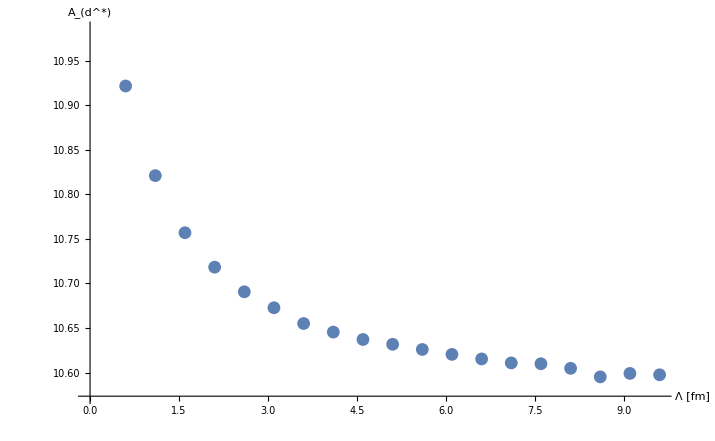

```mathematica
ListPlot[Transpose[{Λl,addstars}],AxesLabel->{"Λ [fm]","A_(d^*)"}]
```